## Import Data

#### CO2 Data

We will work with three data-sets for the CO2 analysis. The data collection is conducted by the NOAA in conjunction with the GML.

```mathematica
globalTrend=Import[NotebookDirectory[]<>"/co2_trend_gl.csv"]; 
annualCO2 = Import[NotebookDirectory[]<>"/co2_annmean_mlo.csv"];
monthlyCO2 = Import[NotebookDirectory[]<>"/co2_mm_mlo.csv"];
```

## Data cleaning

We examine each of the three data-sets. The first lines of the csv contain meta-data, which explains data along with usage . The data of interest seems to be on line x for each of the dataset. We will overwrite the data to begin at this data-point.

Global Trend,  x = 61.

Annual CO2, x = 56.

Monthly CO2, x = 52.

```mathematica
globalTrend//Dataset
annualCO2//Dataset
monthlyCO2//Dataset
```

Overwrite the existing data-sets and inspect the head object of the data.

```mathematica
globalTrend = globalTrend[[61;;, ;;]];
annualCO2 = annualCO2[[56;;, ;;]];
monthlyCO2 = monthlyCO2[[52;;, ;;]];
```

```mathematica
globalTrend[[;;6, ;;]]//Dataset
annualCO2[[;;6, ;;]]//Dataset
monthlyCO2[[;;6, ;;]]//Dataset
```

## CO2 Global Trend

#### Estimated CO2 Daily Global Seasonal Cycle and Trend (ppm) over the last ten years.

The global trend in CO2 over the last ten years are displayed below.

```mathematica
globalTrend//Dimensions
globalTrend[[;;6,;;]]//Dataset
```

{3860,5}

Create the variables for smoothed and trend data from the data-set.

```mathematica
smoothed = globalTrend[[2;;,4]]; (* All rows, 4th column *)
trend = globalTrend[[2;;,5]];
```

```mathematica
summary[smoothed]
```

{389.16,397.88,404.754,411.33,419.1}

Create tick list for the plot.

```mathematica
Range[100, 3750, 365]
```

{100,465,830,1195,1560,1925,2290,2655,3020,3385,3750}

```mathematica
globalTrend[[100,1]];
globalTrend[[465,1]];
globalTrend[[830,1]];
globalTrend[[1195,1]];
globalTrend[[1560,1]];
globalTrend[[1925,1]];
globalTrend[[2290,1]];
globalTrend[[2655,1]];
globalTrend[[3020,1]];
globalTrend[[3385,1]];
globalTrend[[3750,1]];
```

```mathematica
smoothed = globalTrend[[;;,4]]; (* All rows, 4th column *)
trend = globalTrend[[;;,5]];
```

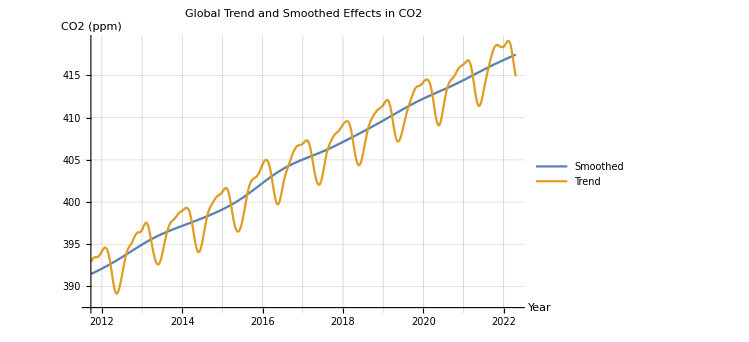

```mathematica
tickList = {{100, "2012"}, {465, "2013"}, {830, "2014"}, {1195, "2015"}, {1560, "2016"}, {1925, "2017"}, {2290, "2018"}, {2655, "2019"}, {3020, "2020"}, {3385,"2021"}, {3750,"2022"}};
ListLinePlot[{trend, smoothed},  PlotLegends->{"Smoothed", "Trend" }, PlotLabel->"Global Trend and Smoothed Effects in CO2",  AxesLabel->{"Year", "CO2 (ppm)"}, Ticks->{tickList, Automatic}, GridLines->Automatic]
```

```mathematica
LinearFit1=Fit[smoothed,{1,x},x]
```

391.631+0.00679954 x

## Annual mean CO2 at Mauna Loa since 1958

Annual mean CO2 at Mauna Loa Observatory. The CO2 data is collected over time at annual intervals. The trend line is a smooth curve upward over time. This indicates that the seasonality is over the year, and would be seen at monthly intervals.

```mathematica
annualCO2//Dimensions
annualCO2[[;;6, ;;]]//Dataset
```

{64,3}

```mathematica
mean = annualCO2[[2;;, 2]];(* all rows, 2nd column *)
summary[mean]
```

{315.98,330.19,357.338,382.09,416.45}

```mathematica
tickList2 = {{10, "1967"}, {20, "1977"}, {30, "1987"}, {40, "1997"}, {50, "2007"}, {60, "2017"}}
```

{{10,1967},{20,1977},{30,1987},{40,1997},{50,2007},{60,2017}}

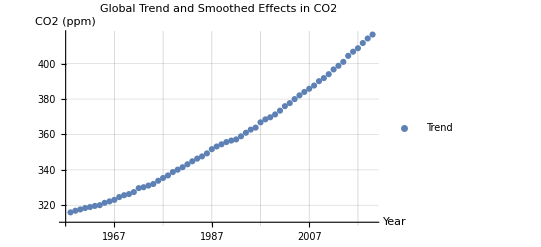

```mathematica
ListPlot[{mean},  PlotLegends->{"Trend", "Smoothed" }, PlotLabel->"Global Trend and Smoothed Effects in CO2",  AxesLabel->{"Year", "CO2 (ppm)"}, Ticks->{tickList2, Automatic}, GridLines->Automatic]
```

## Monthly CO2 Data from Mauna Loa

Monthly data from Mauna Loa. We look at the monthly data in order to better see the seasonality effects in the data.

```mathematica
monthlyCO2//Dimensions
monthlyCO2[[;;6,;;]]//Dataset
```

{773,8}

All years from 1958 to 2022 in monthly intervals.  The third column shows the decimal date. We can delineate the columns in the dataset.

```mathematica
year =  monthlyCO2[[2;;,1]];
average = monthlyCO2[[2;;,4]];
deseasonalised = monthlyCO2[[2;;,5]];
sdev = monthlyCO2[[2;;,7]];
unc = monthlyCO2[[2;;,8]];
```

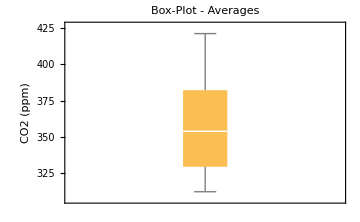

{312.43,329.56,357.278,382.02,420.99}

```mathematica
BoxWhiskerChart[average,ImageSize->Medium,PlotLabel->"Box-Plot - Averages", FrameLabel->{"","CO2 (ppm)"}]
summary[average]
```

### Seasonality within the monthly data

From plotting the average CO2 data, we see there is clearly a trend upwards across time. Evident too is the fact that there is seasonality within the data. We can overlay the de-seasonalised data in order to see clearly the moving average.  Look up seasonality in CO2 in google Scholar.

```mathematica
tickList3 = {{205, "1975"}, {385, "1990"}, {565, "2005"}, {745, "2020"}}
```

{{205,1975},{385,1990},{565,2005},{745,2020}}

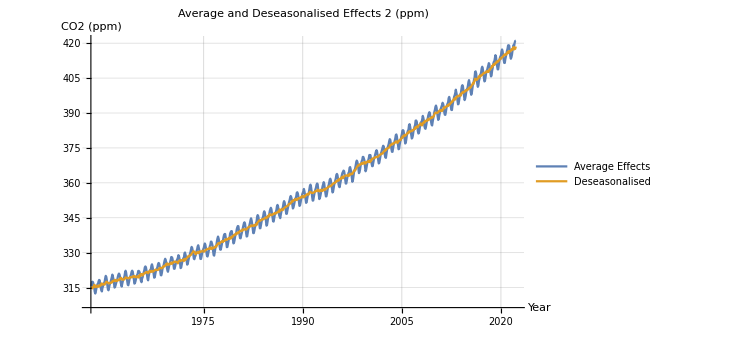

```mathematica
ListLinePlot[{average, deseasonalised},  PlotLegends->{"Average Effects", "Deseasonalised" }, PlotLabel->"Average and Deseasonalised Effects 2 (ppm)", Ticks->{tickList3, Automatic}, AxesLabel->{"Year", "CO2 (ppm)"}, GridLines->Automatic]
```

#### Plot seasonality across the year

1959, 1960, 1961.

```mathematica
monthlyCO2[[12;;23, ;;]]//Dataset;(* 1959 only *)
monthlyCO2[[24;;35, ;;]]//Dataset;
monthlyCO2[[36;;47, ;;]]//Dataset;
average[[12;;23]]; (*1959 *)
average[[24;;35]];(*1960 *)
average[[36;;47]]; (*1961 *)
```

1979, 1980, 1981.

```mathematica
monthlyCO2[[252;;263,;;]]//Dataset;
monthlyCO2[[264;;275,;;]]//Dataset;
monthlyCO2[[276;;287,;;]]//Dataset;
average[[252;;263]] ;(*1979 *)
average[[264;;275]] ;(*1980 *)
average[[276;;287]]; (*1981 *)
```

1999, 2000, 2001.

```mathematica
monthlyCO2[[492;;503,;;]]//Dataset;
monthlyCO2[[504;;515,;;]]//Dataset;
monthlyCO2[[516;;527,;;]]//Dataset;
average[[492;;503]] ;(*1999 *)
average[[504;;515]] ;(*2000 *)
average[[516;;527]]; (*2001 *)
```

2019, 2020, 2021.

```mathematica
monthlyCO2[[732;;743,;;]]//Dataset;
monthlyCO2[[744;;755,;;]]//Dataset;
monthlyCO2[[756;;767,;;]]//Dataset;
average[[732;;743]] ;(*2019 *)
average[[744;;755]] ;(*2020 *)
average[[756;;767]] ;(*2021 *)
```

Look at the five year intervals, rather than 1.

```mathematica
monthlyCO2[[24;;35, ;;]]//Dataset;
monthlyCO2[[84;;95, ;;]]//Dataset;(* 1959 only *)
monthlyCO2[[144;;155, ;;]]//Dataset;
average[[24;;35]]; (*1960 *)
average[[84;;95]];(*1965 *)
average[[144;;155]]; (*1970 *)
```

```mathematica
monthlyCO2[[624;;635, ;;]]//Dataset;
monthlyCO2[[684;;695, ;;]]//Dataset;
monthlyCO2[[744;;755]]//Dataset;
average[[624;;635]]; (*2010 *)
average[[684;;695]] ;(*2015 *)
average[[744;;755]] ;(*2020 *)
```

Now let’s take a look at plotting these four sets of years.

```mathematica
Range[1959, 2019, 20]
```

{1959,1979,1999,2019}

```mathematica
ListPlot[{average[[36;;47]] , average[[24;;35]] ,average[[12;;23]]},  PlotLabels-> {"1961", "1960" , "1959"},PlotLabel->Style["Annual Average Effects CO2 (ppm)", 16], AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[276;;287]], average[[264;;275]] ,average[[252;;263]] },  PlotLabels-> {"1981", "1980" , "1979"}, PlotLabel->Style["Annual Average Effects CO2 (ppm)", 16],AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[516;;527]] , average[[504;;515]] ,average[[492;;503]]},PlotLabels-> {"2001", "2000" , "1999"},   PlotLabel->Style["Annual Average Effects CO2 (ppm)", 16],AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[756;;767]], average[[744;;755]] ,average[[732;;743]] },PlotLabels-> {"2021", "2020" , "2019"},  PlotLabel->Style["Annual Average Effects CO2 (ppm)", 16],AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Comparing  1960 and 2020, we see the seasonal effects of 1960 are diminished by the larger effects of 2020. The CO2 levels for 2020 are 100 ppm higher than CO2 levels for 1960.

```mathematica
ListPlot[{  average[[744;;755]], average[[24;;35]]  },PlotLabels-> {"2020" , "1960"},  PlotLabel->Style["Annual Average Effects CO2", 16],AxesLabel->{"Month","CO2"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

Despite not appearing so, CO2 data from 2020 still forms strong peaks and troughs, which is muted out somewhat when compared against different time periods.

```mathematica
ListPlot[{  average[[744;;755]]},PlotLabels-> {"2020" , "1960"},  PlotLabel->Style["Annual Average Effects CO2", 16],AxesLabel->{"Month","CO2"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

```mathematica
ListPlot[{average[[144;;157]] , average[[84;;95]] ,average[[24;;35]]},  PlotLabels-> {"1970", "1965" , "1960"},PlotLabel->Style["Annual Average Effects CO2 (ppm)", 16], AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[744;;755]], average[[684;;695]] ,average[[624;;635]] },PlotLabels-> {"2020", "2015" , "2010"},  PlotLabel->Style["Annual Average Effects CO2 (ppm)", 16],AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

-Graphics-

## Standard deviation

Create the upper and lower bounds.

```mathematica
Count[sdev, -9.99]
sdev = ReplaceAll[sdev, -9.99 -> 0];
```

196

```mathematica
UB = average + sdev;
LB = average - sdev;
```

```mathematica
summary[average]
summary[UB]
summary[LB]
```

{312.43,329.56,357.278,382.02,420.99}

{312.43,329.69,357.651,382.4,421.75}

{312.43,329.35,356.905,381.6,420.69}

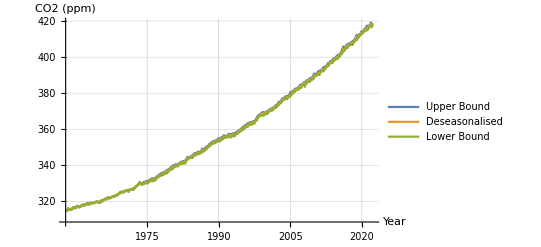

```mathematica
ListLinePlot[{deseasonalised + sdev,deseasonalised,  deseasonalised - sdev},Ticks->{tickList3, Automatic}, AxesLabel->{"Year", "CO2 (ppm)"},   PlotLegends->{"Upper Bound", "Deseasonalised" , "Lower Bound"}, GridLines->Automatic]
```

Let’s look at 2010 to 2020 only.

```mathematica
UB10 = UB[[624;;755]];
LB10 = LB[[624;;755]];
avg10 = average[[624;;755]];
```

```mathematica
tickList4 = {{24, "2012"}, {48, "2014"}, {72, "2016"}, {96, "2018"}, {120, "2020"}};
```

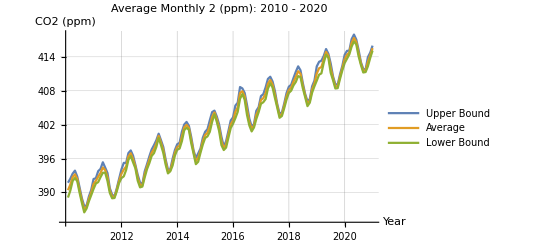

```mathematica
ListLinePlot[{UB10,avg10,  LB10}, AxesLabel->{"Year", "CO2 (ppm)"},   PlotLabel->"Average Monthly 2 (ppm): 2010 - 2020",  PlotLegends->{"Upper Bound", "Average" , "Lower Bound"}, Ticks->{tickList4, Automatic}, GridLines->Automatic]
```

```mathematica
UBD10 = deseasonalised[[624;;755]] + sdev[[624;;755]];
LBD10 = deseasonalised[[624;;755]] - sdev[[624;;755]];
deseasonalised10 = deseasonalised[[624;;755]];
```

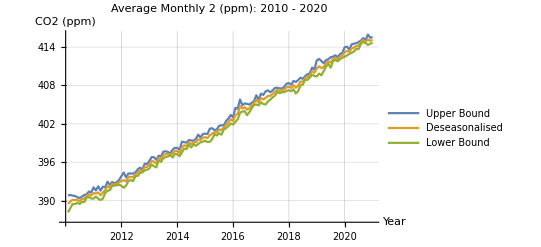

```mathematica
ListLinePlot[{UBD10,deseasonalised10,  LBD10}, AxesLabel->{"Year", "CO2 (ppm)"},     PlotLabel->"Average Monthly 2 (ppm): 2010 - 2020",  PlotLegends->{"Upper Bound", "Deseasonalised" , "Lower Bound"}, Ticks->{tickList4, Automatic}, GridLines->Automatic]
```